-(1.8368×10^-7 (0.64-Energy)^2 Energy^2)/(1-ⅇ^(0.816594 √Energy))

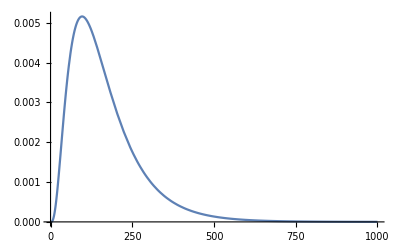

-381.324

```mathematica
Clear["Global`*"]
NdE[Energy_/; Energy>=0]=Normalize[A*((-0.6295*36*π)/137)*(Energy^2*(0.64-Energy)^2)/(1-Exp[(36*π)/137*√(Energy/(2*.511))]), Integrate[#, {Energy, 0, Infinity}]&]
Plot[NdE[Energy], {Energy, 0, 1000}]
```

```mathematica
Integrate[((1.8367961863213326*10^-7 )*(0.64-Energy)^2 *Energy^2)/(1-ⅇ^(0.8165943268408818* √Energy)), {Energy, 0, Infinity}]
```

1.02419